{A_0→-56/3,A_1→29/4,A_2→16}

{-296/3-(56 X)/3,5+(29 X)/4,5+16 X}

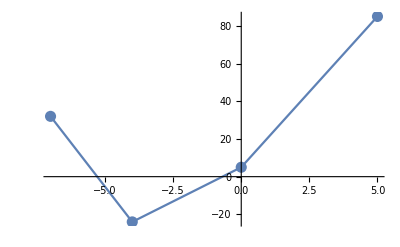

```mathematica
Subscript[x, 0]=-7;Subscript[x, 1]=-4;Subscript[x, 2]=0;Subscript[x, 3]=5;
Subscript[f, 0]= 32;Subscript[f, 1]=-24;Subscript[f, 2]=5;Subscript[f, 3]=85;
n=3;
Subscript[P, k_][X_]=Subscript[f, k]+ (X-Subscript[x, k])*Subscript[A, k];
eq1=Table[Subscript[P, k][Subscript[x, k+1]]==Subscript[P, k+1][Subscript[x, k+1]],{k,0,n-2}];
eq2={Subscript[P, n-1][Subscript[x, n]]==Subscript[f, n]};
eq=Join[eq1,eq2];
koef=Solve[eq,{}]//Flatten
Spl[X_]=Table[Subscript[P, k][X]/.koef,{k,0,n-1}]//Expand
Tb1=Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}];
Gr1= ListPlot[Tb1,PlotStyle->{PointSize[0.02]}];
Gr2=Table[Plot[Spl[X][[k]],{X,Subscript[x, k-1],Subscript[x, k]}],{k,1,n}];
Show[Gr1,Gr2]
```